26. Find the possible behaviors of a Turing machine with 2 states and 2 colors on a blank tape.

```mathematica
(* number of possible rules: *)
```

```mathematica
8^4
```

4096

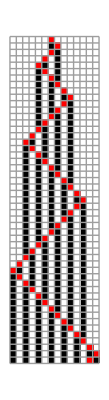

```mathematica
ArrayPlot[Function[u,MapAt[Red&,u[[2]],u[[1,2]]]]/@TuringMachine[2506,{1,{{},0}},50],Mesh->True]
```

```mathematica
ArrayPlot[Last /@ TuringMachine[2506,{1,{{},0}},50], Mesh->True]
```

-Graphics-

```mathematica
Table[ArrayPlot[Last/@TuringMachine[n,{1,{{},0}},40],ImageSize->{Automatic,80}],{n,2500,2520}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* some interesting rules: *)
```

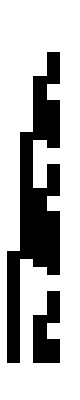
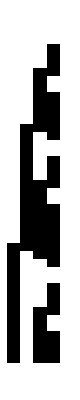
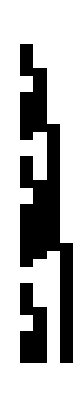
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot[Last/@TuringMachine[#,{1,{{},0}},40]]& /@ {819,899,1512,1530,1953,1971,4003}
```

```mathematica
(* some examples. behaviors: 
- trivial: all white
- white triangle (with black edge)
- black triangle
- vertical lines (with triangular growth)
- veritcal line (without growth)
- less trivial ... *)
```

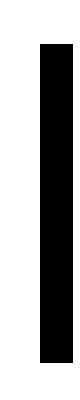
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ArrayPlot[Last/@TuringMachine[n,{1,{{},0}},40],ImageSize->{Automatic,80}],{n,400,450}]
```

```mathematica
(* I'll show some rules *)
```

```mathematica
ShowRule[oldvalue_,newvalue_,oldstate_,newstate_,offset_,colorrule_List]:=Print[LongRightArrow[{Image[ArrayPlot[{oldvalue},Mesh->True,MeshStyle->Black,ColorRules->colorrule],ImageSize->{Length[oldvalue]*25,25}],Image[Rasterize[Graphics[{Thickness[.05],Arrowheads[.3],Arrow[{{0,0},{0,oldstate}}]}]],ImageSize->{Automatic,25}]},{Image[ArrayPlot[{newvalue},Mesh->True,MeshStyle->Black,ColorRules->colorrule],ImageSize->{Length[newvalue]*25,25}],Image[Rasterize[Graphics[{Thickness[.05],Arrowheads[.3],Arrow[{{0,0},{0,newstate}}]}]],ImageSize->{Automatic,25}],offset}]]
```

```mathematica
ShowRule[{0},{0},-1,-1,#,{1->Black,0->LightGray}]& @@@ {{-1},{1}}
```

{-Graphics-,-Graphics-}⟶{-Graphics-,-Graphics-,-1}

{-Graphics-,-Graphics-}⟶{-Graphics-,-Graphics-,1}

{Null,Null}

```mathematica
ShowRule[{0},{0},-1,1,#,{1->Black,0->LightGray}]& @@@ {{-1},{1}}
```

{-Graphics-,-Graphics-}⟶{-Graphics-,-Graphics-,-1}

{-Graphics-,-Graphics-}⟶{-Graphics-,-Graphics-,1}

{Null,Null}

```mathematica
ShowRule[{0},{0},1,1,#,{1->Black,0->LightGray}]& @@@ {{-1},{1}}
```

{-Graphics-,-Graphics-}⟶{-Graphics-,-Graphics-,-1}

{-Graphics-,-Graphics-}⟶{-Graphics-,-Graphics-,1}

{Null,Null}

```mathematica
ShowRule[{0},{0},1,-1,#,{1->Black,0->LightGray}]& @@@ {{-1},{1}}
```

{-Graphics-,-Graphics-}⟶{-Graphics-,-Graphics-,-1}

{-Graphics-,-Graphics-}⟶{-Graphics-,-Graphics-,1}

{Null,Null}

```mathematica
ShowRule[{0},{1},1,-1,#,{1->Black,0->LightGray}]& @@@ {{-1},{1}}
```

{-Graphics-,-Graphics-}⟶{-Graphics-,-Graphics-,-1}

{-Graphics-,-Graphics-}⟶{-Graphics-,-Graphics-,1}

{Null,Null}

```mathematica
ShowRule[{0},{1},1,1,#,{1->Black,0->LightGray}]& @@@ {{-1},{1}}
```

{-Graphics-,-Graphics-}⟶{-Graphics-,-Graphics-,-1}

{-Graphics-,-Graphics-}⟶{-Graphics-,-Graphics-,1}

{Null,Null}

```mathematica
(* etc *)
```